# Creating, Accessing, and Modifying Lists

Math 250 - Mathematical Computing
Christopher Hanusa

## 3.1 Aim

We develop tools for creating, accessing, and modifying lists.

Tip: You can evaluate ALL cells in this file in order using the Evaluation > Evaluate Notebook command.

## 3.2 The Table command, Part Deux

### More Complicated Functions

The Table command is much more powerful than simply creating lists of numbers.  For instance, you can create lists of anything in the language of Mathematica:

#### Graphics objects:

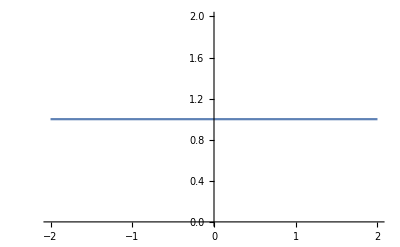


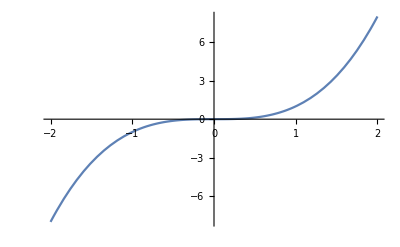
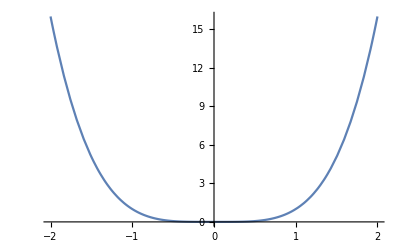
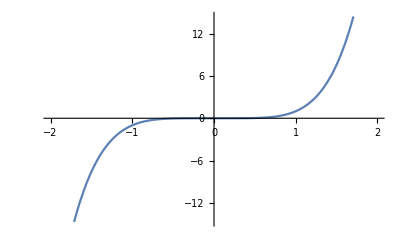
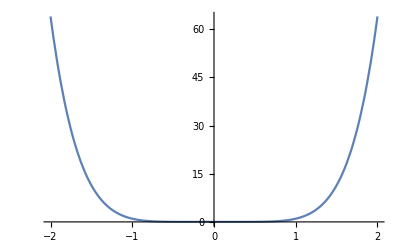
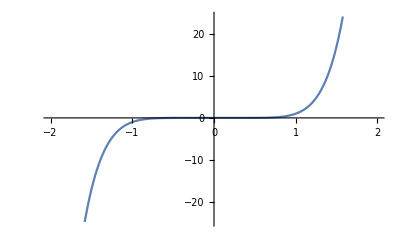
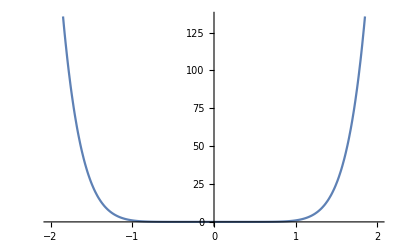
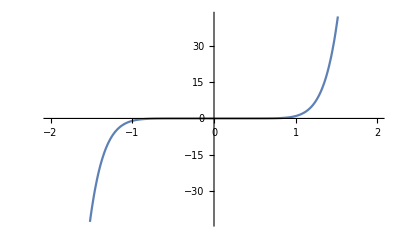

```mathematica
Table[Plot[x^n,{x,-2,2}],{n,0,10}]
```

#### Colors:

```mathematica
colors=Table[ColorData["Rainbow"][x],{x,0,1,.05}]
```

{RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.3431304, 0.11581720000000001, 0.6369784000000001],RGBColor[0.2748608, 0.18226360000000003, 0.7272788],RGBColor[0.2480688, 0.27972840000000004, 0.7879248],RGBColor[0.2484884, 0.3863264, 0.813373],RGBColor[0.266122, 0.486664, 0.802529],RGBColor[0.29795960000000005, 0.5657928, 0.7522386],RGBColor[0.33865560000000006, 0.6276854000000001, 0.6832816],RGBColor[0.38822480000000004, 0.674195, 0.6035436],RGBColor[0.44655700000000004, 0.7074632, 0.5203932],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.5888042000000001, 0.7409584, 0.3750068],RGBColor[0.6660832000000002, 0.7430418, 0.32293539999999993],RGBColor[0.7408424, 0.7340177999999999, 0.28383179999999997],RGBColor[0.8083416, 0.7110806, 0.255976],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.8935136, 0.6004149999999999, 0.2205464],RGBColor[0.9021174, 0.5055087999999998, 0.20182519999999995],RGBColor[0.8929546, 0.38966159999999994, 0.1794008],RGBColor[0.8739574, 0.26078759999999984, 0.1548104],RGBColor[0.857359, 0.131106, 0.132128]}

```mathematica
Length[colors]
```

21

#### The Periodic Table of the Elements:

```mathematica
Table[ElementData[i,"Abbreviation"],{i,1,100}]
```

{H,He,Li,Be,B,C,N,O,F,Ne,Na,Mg,Al,Si,P,S,Cl,Ar,K,Ca,Sc,Ti,V,Cr,Mn,Fe,Co,Ni,Cu,Zn,Ga,Ge,As,Se,Br,Kr,Rb,Sr,Y,Zr,Nb,Mo,Tc,Ru,Rh,Pd,Ag,Cd,In,Sn,Sb,Te,I,Xe,Cs,Ba,La,Ce,Pr,Nd,Pm,Sm,Eu,Gd,Tb,Dy,Ho,Er,Tm,Yb,Lu,Hf,Ta,W,Re,Os,Ir,Pt,Au,Hg,Tl,Pb,Bi,Po,At,Rn,Fr,Ra,Ac,Th,Pa,U,Np,Pu,Am,Cm,Bk,Cf,Es,Fm}

#### Coordinates of the vertices of a polygon:

{{1,0},{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2}}

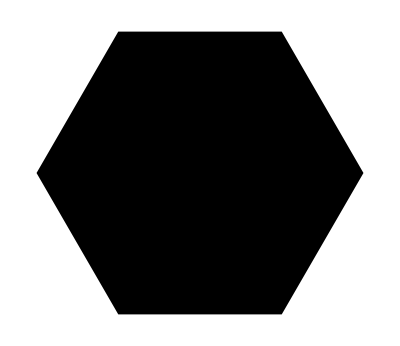

```mathematica
vertices=Table[{Cos[2π k/6],Sin[2π k/6]},{k,0,5}]
Graphics[Polygon[vertices]]
```

{{1,0},{1/4 (-1+√5),√(5/8+(√5)/8)},{1/4 (-1-√5),√(5/8-(√5)/8)},{1/4 (-1-√5),-√(5/8-(√5)/8)},{1/4 (-1+√5),-√(5/8+(√5)/8)}}

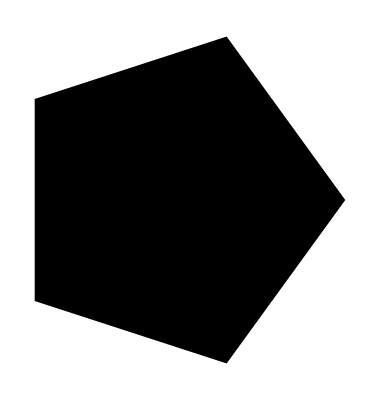

```mathematica
vertices=Table[{Cos[2π k/5],Sin[2π k/5]},{k,0,4}]
Graphics[Polygon[vertices]]
```

#### A list of such a polygons:

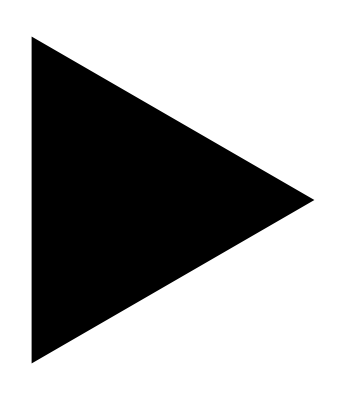
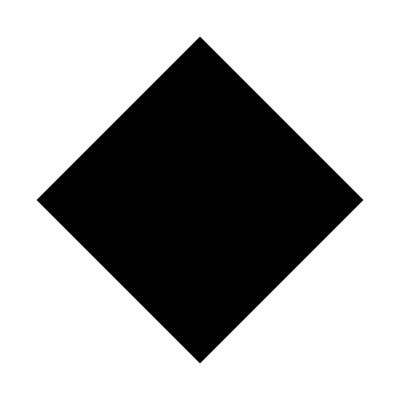
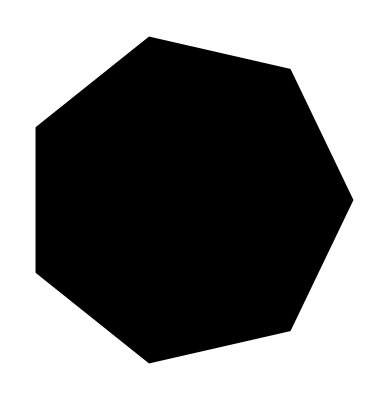
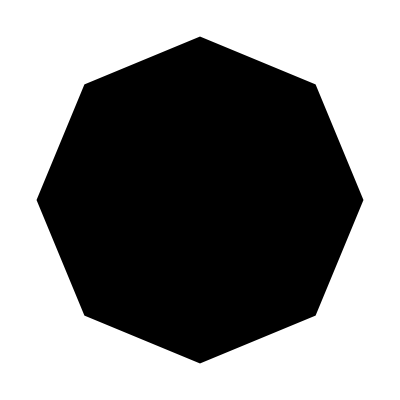
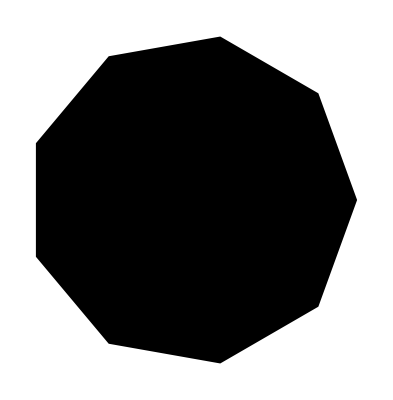
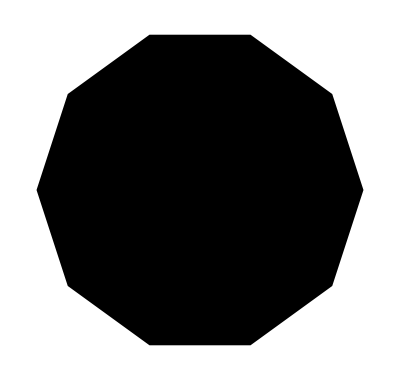
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Polygon[Table[{Cos[2π k/i],Sin[2π k/i]},{k,0,i-1}]]],{i,3,10}]
```

### More Variables

The Table command can also create a list as a function of two or more variables changing at a time.

```mathematica
array=Table[x*y,{x,3},{y,5}]
```

{{1,2,3,4,5},{2,4,6,8,10},{3,6,9,12,15}}

Read this Table command as:

"Create a table of values of the form x times y, where x ranges from 1 to 3 and y ranges from 1 to 5.”

Example 3.2.1. What do the following commands do?

```mathematica
Table[{x,y},{x,2,4},{y,5,7}]
```

{{{2,5},{2,6},{2,7}},{{3,5},{3,6},{3,7}},{{4,5},{4,6},{4,7}}}

```mathematica
Table[IntegerString[x,"Roman"],{x,100}]
```

{I,II,III,IV,V,VI,VII,VIII,IX,X,XI,XII,XIII,XIV,XV,XVI,XVII,XVIII,XIX,XX,XXI,XXII,XXIII,XXIV,XXV,XXVI,XXVII,XXVIII,XXIX,XXX,XXXI,XXXII,XXXIII,XXXIV,XXXV,XXXVI,XXXVII,XXXVIII,XXXIX,XL,XLI,XLII,XLIII,XLIV,XLV,XLVI,XLVII,XLVIII,XLIX,L,LI,LII,LIII,LIV,LV,LVI,LVII,LVIII,LIX,LX,LXI,LXII,LXIII,LXIV,LXV,LXVI,LXVII,LXVIII,LXIX,LXX,LXXI,LXXII,LXXIII,LXXIV,LXXV,LXXVI,LXXVII,LXXVIII,LXXIX,LXXX,LXXXI,LXXXII,LXXXIII,LXXXIV,LXXXV,LXXXVI,LXXXVII,LXXXVIII,LXXXIX,XC,XCI,XCII,XCIII,XCIV,XCV,XCVI,XCVII,XCVIII,XCIX,C}

Example 3.2.2. How do you generate the following output?

```mathematica
{{{0,0},{0,1},{0,2}},
{{1,0},{1,1},{1,2}},
{{2,0},{2,1},{2,2}}}
```

```mathematica
Table[{x,y,z},{x,0,2},{y,0,2},{z,0,2}]
```

{{{{0,0,0},{0,0,1},{0,0,2}},{{0,1,0},{0,1,1},{0,1,2}},{{0,2,0},{0,2,1},{0,2,2}}},{{{1,0,0},{1,0,1},{1,0,2}},{{1,1,0},{1,1,1},{1,1,2}},{{1,2,0},{1,2,1},{1,2,2}}},{{{2,0,0},{2,0,1},{2,0,2}},{{2,1,0},{2,1,1},{2,1,2}},{{2,2,0},{2,2,1},{2,2,2}}}}

IntegerName takes a number and gives out its English name.

```mathematica
Table[IntegerName[x],{x,100}]
```

{one,two,three,four,five,six,seven,eight,nine,ten,eleven,twelve,thirteen,fourteen,fifteen,sixteen,seventeen,eighteen,nineteen,twenty,twenty-one,twenty-two,twenty-three,twenty-four,twenty-five,twenty-six,twenty-seven,twenty-eight,twenty-nine,thirty,thirty-one,thirty-two,thirty-three,thirty-four,thirty-five,thirty-six,thirty-seven,thirty-eight,thirty-nine,forty,forty-one,forty-two,forty-three,forty-four,forty-five,forty-six,forty-seven,forty-eight,forty-nine,fifty,fifty-one,fifty-two,fifty-three,fifty-four,fifty-five,fifty-six,fifty-seven,fifty-eight,fifty-nine,sixty,sixty-one,sixty-two,sixty-three,sixty-four,sixty-five,sixty-six,sixty-seven,sixty-eight,sixty-nine,seventy,seventy-one,seventy-two,seventy-three,seventy-four,seventy-five,seventy-six,seventy-seven,seventy-eight,seventy-nine,eighty,eighty-one,eighty-two,eighty-three,eighty-four,eighty-five,eighty-six,eighty-seven,eighty-eight,eighty-nine,ninety,ninety-one,ninety-two,ninety-three,ninety-four,ninety-five,ninety-six,ninety-seven,ninety-eight,ninety-nine,one hundred}

```mathematica
{10,100,1000,10000}
```

```mathematica
{10^1,10^2,10^3,10^4}
```

```mathematica
Table[10^i,{i,4}]
```

{10,100,1000,10000}

```mathematica
Table[IntegerName[10^i,"Words"],{i,4}]
```

{ten,one hundred,one thousand,ten thousand}

```mathematica
{"ten","one hundred","one thousand","ten thousand"}
```

## 3.3 Flatten

The number of braces that can accumulate in Mathematica can be overwhelming.
When you want to remove extra braces from nested lists, use the Flatten command.

```mathematica
list=Table[x*y,{x,3},{y,3}]
```

{{1,2,3},{2,4,6},{3,6,9}}

```mathematica
Flatten[list]
```

{1,2,3,2,4,6,3,6,9}

You can also specify how many layers of braces you want to remove.  For example, if your goal is to create a set of coordinate pairs (for points on a picture, for instance), then you wouldn’t want to remove all of the braces.

{{{2,0},{3,1},{4,2}},{{5/2,-1/2},{7/2,1/2},{9/2,3/2}},{{3,-1},{4,0},{5,1}},{{7/2,-3/2},{9/2,-1/2},{11/2,1/2}},{{4,-2},{5,-1},{6,0}},{{9/2,-5/2},{11/2,-3/2},{13/2,-1/2}},{{5,-3},{6,-2},{7,-1}},{{11/2,-7/2},{13/2,-5/2},{15/2,-3/2}},{{6,-4},{7,-3},{8,-2}}}

{{2,0},{3,1},{4,2},{5/2,-1/2},{7/2,1/2},{9/2,3/2},{3,-1},{4,0},{5,1},{7/2,-3/2},{9/2,-1/2},{11/2,1/2},{4,-2},{5,-1},{6,0},{9/2,-5/2},{11/2,-3/2},{13/2,-1/2},{5,-3},{6,-2},{7,-1},{11/2,-7/2},{13/2,-5/2},{15/2,-3/2},{6,-4},{7,-3},{8,-2}}

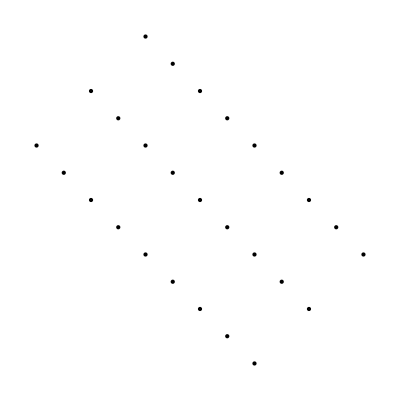

```mathematica
list2=Table[{{1,1},{-1,1}}.{x,y},{x,1,5,1/2},{y,3}]
coords=Flatten[list2,1]
Graphics[Point[coords]]
```

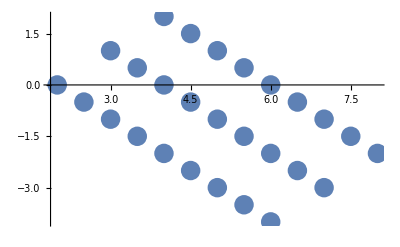

```mathematica
ListPlot[coords,PlotMarkers->{Automatic,Large}]
```

```mathematica
Flatten[list2]
```

{1,1,1,2,1,3,2,1,2,2,2,3,3,1,3,2,3,3,4,1,4,2,4,3,5,1,5,2,5,3}

Instead, use the optional second argument to only remove one set of braces.

```mathematica
coords=Flatten[list2,1]
```

{{1,2},{1,3},{1,4},{3/2,5/2},{3/2,7/2},{3/2,9/2},{2,3},{2,4},{2,5},{5/2,7/2},{5/2,9/2},{5/2,11/2},{3,4},{3,5},{3,6},{7/2,9/2},{7/2,11/2},{7/2,13/2},{4,5},{4,6},{4,7},{9/2,11/2},{9/2,13/2},{9/2,15/2},{5,6},{5,7},{5,8}}

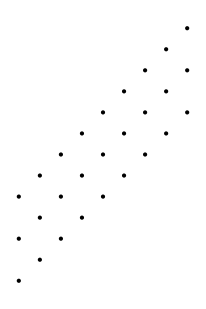

```mathematica
Graphics[Point[coords]]
```

Example 3.3.1. What will this command give?

```mathematica
Flatten[{{{{1},2},3},4}]
```

{1,2,3,4}

Example 3.3.2. What command will give {{{1},2},3,4}?

```mathematica
Flatten[{{{{1},2},3},4},3]
```

{1,2,3,4}

## 3.4 Join

How do you combine two lists?  Use Join.

```mathematica
list1={a,b,c}
list2={1,2,3}
```

{a,b,c}

{1,2,3}

```mathematica
Join[list1,list2]
```

{a,b,c,1,2,3}

Example 3.4.1.  Create a list with the first 10 positive even numbers followed by the first 10 positive odd numbers.

```mathematica
evens=Table[2*i,{i,1,10}]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
odds=Table[2*i-1,{i,1,10}]
```

{1,3,5,7,9,11,13,15,17,19}

```mathematica
Join[evens,odds]
```

{2,4,6,8,10,12,14,16,18,20,1,3,5,7,9,11,13,15,17,19}

## 3.5 Append and Prepend

To add an element to the end of a list, use Append.  To add an element to the beginning, use Prepend.

```mathematica
powersOfTen=Table[10^i,{i,0,5}]
```

{1,10,100,1000,10000,100000}

```mathematica
Append[powersOfTen,10^6]
```

{1,10,100,1000,10000,100000,1000000}

```mathematica
powersOfTen
```

{1,10,100,1000,10000,100000}

```mathematica
Prepend[powersOfTen,10^-1]
```

{1/10,1,10,100,1000,10000,100000}

```mathematica
powersOfTen
```

{1,10,100,1000,10000,100000}

You can see that powersOfTen does not change when using Append or Prepend. 
Either redefine powersOfTen or use AppendTo or PrependTo.

```mathematica
powersOfTen=Append[powersOfTen,10^6]
```

{1,10,100,1000,10000,100000,1000000}

```mathematica
PrependTo[powersOfTen,10^-1]
```

{1/10,1,10,100,1000,10000,100000,1000000}

```mathematica
powersOfTen
```

{1/10,1,10,100,1000,10000,100000,1000000}

Example 3.5.1. What will the following command do?

```mathematica
Append[{1,2,3,4},{5,6}]
```

{1,2,3,4,{5,6}}

```mathematica
Join[{1,2,3,4},{5,6}]
```

{1,2,3,4,5,6}

```mathematica
Flatten[Append[{1,2,3,4},{5,6}]]
```

{1,2,3,4,5,6}

## 3.6 Accessing parts of lists

### One entry of a list

It is often useful to access one or more of the entries of a list.  For this we use double square brackets [[n]], which is the shorthand notation for the command Part.

This is the list of the first 100 prime numbers.

```mathematica
primes=Table[Prime[n],{n,100}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

What is the 40th prime number?

```mathematica
primes[[40]]
```

173

```mathematica
Prime[40]
```

173

```mathematica
Part[primes,40]
```

173

### One entry of an array

When the list is a nested list, you can reference an entry of the list to choose a sublist, or any entry of any sublist.

```mathematica
nestedList={{1,2},{3,4},{5,6}};
```

```mathematica
nestedList[[2]]
```

{3,4}

```mathematica
nestedList[[2]][[1]]
```

3

```mathematica
nestedList[[2,1]]
```

3

A deeper nested list

```mathematica
veryverydeeplist = {{{{{a,b},{c,d}},{{e,f},{g,h}}},{{{i,j},{k,l}},{{m,n},{o,p}}}},{{{{q,r},{s,t}},{{u,v},{w,x}}},{{{y,z},{α,β}},{{γ,δ},{ϵ,ζ}}}}}
```

{{{{{a,b},{c,d}},{{e,f},{g,h}}},{{{i,j},{k,l}},{{m,n},{o,p}}}},{{{{q,r},{s,t}},{{u,v},{w,x}}},{{{y,z},{α,β}},{{γ,δ},{ϵ,ζ}}}}}

```mathematica
veryverydeeplist[[2]]
```

{{{{q,r},{s,t}},{{u,v},{w,x}}},{{{y,z},{α,β}},{{γ,δ},{ϵ,ζ}}}}

```mathematica
veryverydeeplist[[2,2]]
```

{{{y,z},{α,β}},{{γ,δ},{ϵ,ζ}}}

```mathematica
veryverydeeplist[[2,2,1]]
```

{{y,z},{α,β}}

```mathematica
veryverydeeplist[[2,2,1,2]]
```

{α,β}

```mathematica
veryverydeeplist[[2,2,1,2,1]]
```

α

### Multiple entries of a list

To extract multiple entries from a list, you can put a list of indices in the double square brackets.

```mathematica
primes[[{3,5,7}]]
```

{5,11,17}

```mathematica
primes[[Range[3,7]]]
```

{5,7,11,13,17}

### Multiple entries of an array

To choose certain rows and columns of an array you can also use sets.  If you want all of the rows and only some of the columns (or vice versa), use the variable “All”.

```mathematica
products=Table[x*y^2,{x,1,10},{y,1,10}];
TableForm[products]
```

1 | 4 | 9 | 16 | 25 | 36 | 49 | 64 | 81 | 100
2 | 8 | 18 | 32 | 50 | 72 | 98 | 128 | 162 | 200
3 | 12 | 27 | 48 | 75 | 108 | 147 | 192 | 243 | 300
4 | 16 | 36 | 64 | 100 | 144 | 196 | 256 | 324 | 400
5 | 20 | 45 | 80 | 125 | 180 | 245 | 320 | 405 | 500
6 | 24 | 54 | 96 | 150 | 216 | 294 | 384 | 486 | 600
7 | 28 | 63 | 112 | 175 | 252 | 343 | 448 | 567 | 700
8 | 32 | 72 | 128 | 200 | 288 | 392 | 512 | 648 | 800
9 | 36 | 81 | 144 | 225 | 324 | 441 | 576 | 729 | 900
10 | 40 | 90 | 160 | 250 | 360 | 490 | 640 | 810 | 1000

Here we choose rows three, four and five, and columns 2, 4, and 8:

```mathematica
products[[Range[3,5],{2,4,8}]]
```

{{12,48,192},{16,64,256},{20,80,320}}

Here we choose the second entries of every row:

```mathematica
products[[All,2]]
```

{4,8,12,16,20,24,28,32,36,40}

Or the third entry of every column:

```mathematica
products[[3,All]]
```

{3,12,27,48,75,108,147,192,243,300}